```mathematica
(* 
This notebook examines the case in which we assume 𝔊=(1-α (R)) and human wealth is finite (α > 1)
*)
(* The RIC holds because Þ/R < 1 *) 
(* The GICTBS says (((R)β(1-℧))^(1/ρ)/Γ) < 1 *)
(* The FHWC-Γ  holds because Γ = (1-α ℧) (R)/(1-℧) ≤ (R) for α > 1 *)
(* The FHWC-PF holds because 𝔊 = (1-α ℧) (R) < (R) for α > 1 *)
(* The GIC-PF may fail because with 𝔊 ≤ R, Þ/(R) < 1 does not imply  Þ/𝔊 < 1 *)
(* The GIC-Γ  may fail because Γ=𝔊/(1-℧)>𝔊 so Þ/Γ = Þ(1-℧)/𝔊 < Þ/𝔊 *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
βMax=βMaxWhereRICHoldsExactly=(R)^(ρ-1);
ϑMin=ϑMinWhereRICHoldsExactly=(βMaxWhereRICHoldsExactly)^-1-1;
(* (((R)β(1-℧))^(1/ρ)/Γ) < 1 *) 
(* (((R)β(1-℧))^(1/ρ)  ) < Γ *) 
(* (((R)β(1-℧))   )) <((1-α ℧) (R)/(1-℧))^ρ *) 
(*      β            < (R)^(ρ-1)(1-α ℧)^ρ/(1-℧)) *) 
βMaxWhereGICTBSHoldsExactly=(1-℧)^-1(R)^(ρ-1)Γ^ρ; 
ϑMinWhereGICTBSHoldsExactly=(βMaxWhereGICTBSHoldsExactly)^-1-1;
βMaxWhereGICΓHoldsExactly=(R)^(ρ-1)Γ^ρ; 
ϑMinWhereGICΓHoldsExactly=(βMaxWhereGICΓHoldsExactly)^-1-1;
βMaxWhereGIC𝔊HoldsExactly=(R)^(ρ-1)𝔊^ρ; 
ϑMinWhereGIC𝔊HoldsExactly=(βMaxWhereGIC𝔊HoldsExactly)^-1-1;
βMaxWhereExistsTargetMatchesGICΓ=(R)^(ρ-1)(1-((α-1)℧)/(1-℧))^ρ;
ϑMinWhereExistsTargetMatchesGICΓ=(βMaxWhereExistsTargetMatchesGICΓ)^-1-1;

(* To use the definition below, apply ReleaseHold[ϑMinRequiredForTargetToExist] to evaluate at the ambient parameter values *)
ϑMinRequiredForTargetToExist = Hold[Clear[ϑ];Chop[ϑSeek/. FindRoot[((Log[(μ-1)]-Log[(ℛ-1)])) /. ϑ -> ϑSeek,{ϑSeek,ϑMinWhereExistsTargetMatchesGICΓ}]]];
(* Search for Log to get Mma to find solutions for which μ-1 and ℛ-1 > 0; otherwise it might find solutions for which μ<0 (note that this notebook examines the case when the FHWC-PF holds so that ℛ > 1 *)
ϑMinRequiredForTargetToExistFunc[αVal_] :=Block[{},α=αVal; Clear[ϑ];Chop[ϑSeek/. FindRoot[(Log[(μ-1)]-Log[(ℛ-1)]) /. ϑ -> ϑSeek,{ϑSeek,ϑBase+0.01}]]];

αWhereϑMinRequiredForTargetToExistStartsToExceedAmbientϑ = Hold[Clear[α];αSeek /. Chop[FindRoot[(α-(1+℧^-1 κ(1-℧)(1+ϖ)^(1/ρ) )/. α->αSeek),{αSeek,1.5}]]];
αWhereϑMinRequiredForTargetToExistStartsToExceedAmbientϑAlt = Hold[Clear[α];αSeek /. Chop[FindRoot[(1+(1-α)℧/(1-℧))-(1+℧((α-1)℧/(κ (1-℧)))^ρ-1)/. α->αSeek,{αSeek,1.5}]]];

<<ManipulatePrepare.m;
Clear[𝔊,𝔤,℧,r,R,ϑ,α];
R =1+(r);
𝔊=(1-α ℧)(R);
𝔤=𝔊-1;
χ=(((α-1)℧)/(κ(1-℧)));
℧=℧Base;
r=rBase+0.07;
ϑ=ϑBase=rBase-0.02;
ÞMinBase=Þ;
ÞRtnBase=ÞRtn;
ÞΓBase=ÞRtnBase (1-℧)/(1-α ℧);
κBase=κ;
ϖBase=(ÞΓBase^-ρ-1)/℧;
α=1.01;
αCuspBase = ReleaseHold[αWhereϑMinRequiredForTargetToExistStartsToExceedAmbientϑ]
```

11.2026

```mathematica
ϑBase
```

0.01

```mathematica
ϑ=ϑBase;
{Clear[α];αSeek /. Chop[FindRoot[(α-(1+℧^-1 κ(1-℧)(1+ϖ)^(1/ρ) )/. α->αSeek),{αSeek,1.5}]]
,Clear[α];αSeek /. Chop[FindRoot[((α-1)-℧^-1 κ(1-℧)(1+ϖ)^(1/ρ) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+ϖ) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+(ÞΓ^-ρ-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn(R)/Γ)^-ρ-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn ℛ)^-ρ-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn)^-ρ ℛ^-ρ-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn)^-ρ ((R)/(R(1-α ℧)(1-℧)^-1))^-ρ-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn)^-ρ (1/((1-α ℧)(1-℧)^-1))^-ρ-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn)^-ρ ((1-℧)^-ρ(1-α ℧)^ρ)-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)^ρ-(℧^-1 κ(1-℧))^ρ(1+((ÞRtn)^-ρ (((1-α ℧)/(1-℧))^ρ)-1)/℧) /. α->αSeek),{αSeek,1.5}]],Clear[α];αSeek /. Chop[FindRoot[((α-1)-(℧^-1 κ(1-℧))(1+((ÞRtn)^-ρ (((1-α ℧)/(1-℧))^ρ)-1)/℧)^(1/ρ) /. α->αSeek),{αSeek,1.5}]]
}
```

{11.2026,11.2026,11.2026,11.2026,11.2026,11.2026,11.2026,11.2026,11.2026,11.2026,11.2026,11.2026}

```mathematica
Clear[ϑ];α=αCuspBase;
{ϑMinWhereRICHoldsExactly,ϑMinWhereΠGreaterZero,ϑMinWhereGICTBSHoldsExactly,ReleaseHold[ϑMinRequiredForTargetToExist]}
```

{-0.0909091,0.00495,-0.0999323,0.01}

```mathematica
Clear[ϑ];ϑ=ϑBase;ReleaseHold[αWhereϑMinRequiredForTargetToExistStartsToExceedAmbientϑ]
```

11.2026

```mathematica
??Chop
```

Chop[expr] replaces approximate real numbers in expr that are close to zero by the exact integer 0.

Attributes[Chop]={Protected}

```mathematica
IntegerPart[αCuspBase]
```

11

```mathematica
εFromInfty=0.001;
Clear[α];
{αLo,αHi}={IntegerPart[αCuspBase],IntegerPart[αCuspBase]+1};
α =αLo;Clear[ϑ];(*ϑMinαLo=Max[ReleaseHold[ϑMinRequiredForTargetToExist],ϑMinWhereRICHoldsExactly]+εFromInfty;*)
ϑMinαLo=ϑBase;
ϑ=ϑMinαLo;FindStableArm;
{𝓂MaxαLo,𝓂MaxMaxαLo}={2,10} 𝓂E;𝒸MaxαLo=cE[𝓂MaxαLo];
```

```mathematica
α =αHi;Clear[ϑ];ϑMinαHi=Max[ReleaseHold[ϑMinRequiredForTargetToExist],ϑMinWhereRICHoldsExactly]+εFromInfty;
```

```mathematica
ϑ=ϑMinαHi;FindStableArm;
{𝓂MaxαHi,𝓂MaxMaxαHi}={2,10} 𝓂E;𝒸MaxαHi=cE[𝓂MaxαHi];

{𝓂MaxPlot,𝓂MaxMaxPlot,𝒸MaxPlot}={Max[𝓂MaxαLo,𝓂MaxαHi],Max[𝓂MaxMaxαLo,𝓂MaxMaxαHi],Max[𝒸MaxαLo,𝒸MaxαHi]}
```

{353.458,1767.29,20.5697}

```mathematica
{𝓂MaxαLo,𝓂MaxαHi}
```

{183.064,353.458}

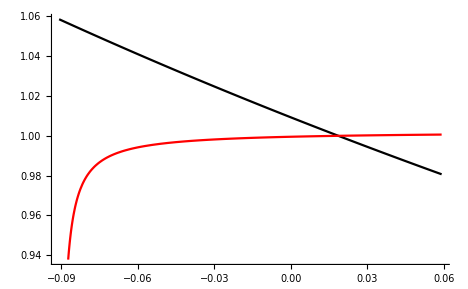

```mathematica
Clear[ϑ];Plot[{ÞΓ /. ϑ -> ϑPlot,(1+℧((((α-1)℧)/(κ(1-℧)))-1))^(-1/ρ)/. ϑ -> ϑPlot},{ϑPlot,ϑMin,ϑMin+0.15},PlotStyle->{Black,Red}]
```

```mathematica
{((μ-1)/μ),((ℛ-1)/ℛ)} /. ϑ -> ϑMinWhereRICHoldsExactly+0.01
```

{0.00652687,0.00351759}

```mathematica
𝒸UnfixedPlot=Plot[d𝒸Eq0SlopeWhereRICHoldsExactly 𝓂Plot,{𝓂Plot,0.,𝓂MaxPlot},PlotStyle->Red];
Clear[ϑ];ϑ=Max[ϑMinWhereRICHoldsExactly,ReleaseHold[ϑMinRequiredForTargetToExist]]+0.01;
```

```mathematica
MatrixForm[{{κ(1+ϖ)^(1/ρ),((α-1)℧)/(1-℧)}
,{(1+ϖ)^(1/ρ),(((α-1)℧)/(κ(1-℧)))}
,{(1+ϖ),(((α-1)℧)/(κ(1-℧)))^ρ}
,{ϖ,(((α-1)℧)/(κ(1-℧)))^ρ-1}
,{(ÞΓ^-ρ-1)℧^-1,(((α-1)℧)/(κ(1-℧)))^ρ-1}
,{(ÞΓ^-ρ-1),℧((((α-1)℧)/(κ(1-℧)))^ρ-1)}
,{ÞΓ^-ρ,1+℧((((α-1)℧)/(κ(1-℧)))^ρ-1)}
,{ÞΓ^-ρ - (1+℧((((α-1)℧)/(κ(1-℧)))^ρ-1)) }
}/. ϑ -> ReleaseHold[ϑMinRequiredForTargetToExist]]
```

({0.0552764,0.0552764}
{1.,1.}
{1.,1.}
{-2.22045×10^-13,2.33147×10^-14}
{-2.22045×10^-13,2.33147×10^-14}
{-1.11022×10^-15,1.16573×10^-16}
{1.,1.}
{-1.2268×10^-15})

```mathematica
FindStableArm
```

```mathematica
ℛ
```

1.00505

```mathematica
{ Π ℛ κ,ℛ-1}
```

{0.0714249,0.00505051}

```mathematica
Clear[ϑ]
```

```mathematica
ÞΓ^-ρ - (1+℧(((α-1)℧)/(κ(1-℧))^ρ-1)) /. ϑ -> ϑBase
```

0.119749

```mathematica
ϑFound = ϑSeek/. FindRoot[ÞΓ^-ρ - (1+℧(((α-1)℧)/(κ(1-℧))^ρ-1)) /. ϑ -> ϑSeek,{ϑSeek,ϑBase}]
```

0.0190572

```mathematica
ϑ=ϑFound
```

0.0190572

```mathematica
?Π
```

Global`Π

Π=((-1+(((R β)^(1/ρ) (1-℧))/𝔊)^-ρ+℧)/℧)^(1/ρ)

```mathematica
(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧
```

-0.796065

```mathematica
{((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ,(((R β)^(1/ρ) (1-℧))/(1+𝔤))^-ρ}
```

{0.99602,0.99602}

```mathematica
(1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ)
```

0.451591

```mathematica
𝓂E2 = (1+((1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤))
```

1.00138

```mathematica
1-((1+r) (1-τ) (1-℧))/(1+𝔤)+((1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤)
```

-0.00367117

```mathematica
ℛ
```

1.00505

```mathematica
Γ+ζ Γ - R
```

-0.00376231

```mathematica
{μ-ℛ}
```

{-0.00367117}

```mathematica
{κ (1+ϖ)^(1/ρ)-(α-1)℧/(1-℧)}
```

{-0.00365272}

```mathematica
ÞΓ
```

1.002

```mathematica
(1-ℛ^-1)
```

0.00502513

```mathematica
?𝓂E
```

Global`𝓂E

𝓂E=(-((1+r) Severance (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤)+(1+((1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤)) (1-Severance ℧))/(1-((1+r) (1-τ) (1-℧))/(1+𝔤)+((1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤))

InterpolatingFunction::dmval: Input value {64.5685} lies outside the range of data in the interpolating function. Extrapolation will be used.

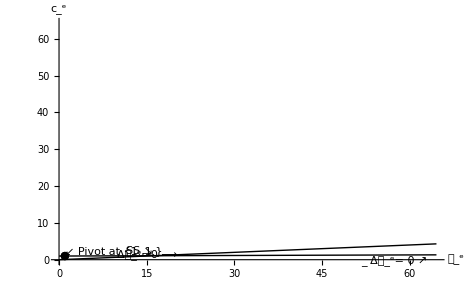

```mathematica
{𝓂MaxPlot,𝓂MaxMaxPlot}={4,10} 𝓂E;𝒸MaxPlot=cE[𝓂MaxPlot];
FindStableArm;
𝓂TargetDiagram[𝓂MaxPlot,𝓂MaxMaxPlot,𝒸MaxPlot]
```

```mathematica
𝓂MaxPlot
```

64.5685

```mathematica
{ÞRtn,ÞΓ} /. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

{0.997421,1.00246}

```mathematica
Π  /. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

0.142806

```mathematica
{℧/(1-℧),κ Π}/. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

{0.00502513,0.000368357}

```mathematica
{-(α+1)℧/(1-℧),κ Π} /. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

{-0.0150754,0.000368357}

```mathematica
{1,κ Π+ℛ^-1}/. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

{1,0.995343}

```mathematica
{ℛ^-1,1+(α+1)℧/(1-℧)}/. ϑ -> ϑMinWhereΠGreaterZero
```

{0.994975,1.01508}

```mathematica
{0.,κ Π +(α+1)℧/(1-℧)}/. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

{0.,0.0154437}

```mathematica
(ÞΓ^-ρ-1)/. ϑ -> ϑMinWhereΠGreaterZero+0.0000001
```

-0.00489803

```mathematica
{(1-℧)^(-1/ρ),ÞΓ} /. ϑ -> ϑMinWhereΠGreaterZero
```

{1.00251,1.00246}

```mathematica
α=-1
```

-1

```mathematica
Π /. ϑ -> ϑMinWhereGICTBSHoldsExactly+0.0000001
```

6.07738×10^-17+0.992511 ⅈ

```mathematica
(μ-1)/μ/. ϑ -> ϑFound
```

0.0666635

```mathematica
α=-1;κ /. ϑ -> ϑMin
```

0.

```mathematica
(R)
```

1.03

```mathematica
ϑMin
```

-0.0291262

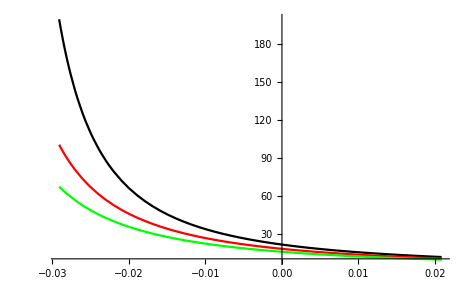

```mathematica
α=0;α0Plot=Plot[𝓂E /. ϑ -> ϑPlot,{ϑPlot,ϑMin,ϑMin+0.05},PlotStyle->{Black},PlotRange->All];
α=1;α1Plot=Plot[𝓂E /. ϑ -> ϑPlot,{ϑPlot,ϑMin,ϑMin+0.05},PlotStyle->{Red},PlotRange->All];
α=2;α2Plot=Plot[𝓂E /. ϑ -> ϑPlot,{ϑPlot,ϑMin,ϑMin+0.05},PlotStyle->{Green},PlotRange->All];
Show[α0Plot,α1Plot,α2Plot,PlotRange->All]
```

```mathematica
Clear[ϑ];α=2;
```

```mathematica
ÞRtn
```

0.985329 (1/(1+ϑ))^0.5

```mathematica
(1-℧)^(1+1/ρ)+(α-1)℧+℧-1
```

0.00250938

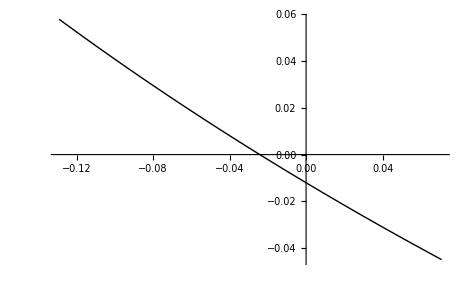

```mathematica
Plot[ÞRtn(1-℧)^(1+1/ρ)+(α-1)℧+℧-1 /. ϑ->ϑPlot,{ϑPlot,ϑMin-0.1,ϑMin+0.1}]
```

```mathematica
ϑMinFound = ϑSeek /. FindRoot[ÞRtn(1-℧)^(1+1/ρ)+(α-1)℧+℧-1 /. ϑ->ϑSeek,{ϑSeek,ϑMin-0.1}]
```

-0.0241982

```mathematica
{ϑMin,ϑMinFound}
```

{-0.0291262,-0.0241982}

```mathematica
κ /. ϑ -> {ϑMin,ϑMinFound}
```

{0.,0.00252832}

```mathematica
𝓂E /. ϑ -> {ϑMin,ϑMinFound}
```

{67.3333,45.8819}

```mathematica
{(μ-1)/μ,(ℛ-1)/ℛ}/. ϑ -> {ϑMin,ϑMinFound}
```

{{0.,0.00704829},-0.0150754}

```mathematica
{1,κ Π + ℛ^-1}/. ϑ -> {ϑMin,ϑMinFound}
```

{1,{1.01508,1.02228}}

```mathematica
ÞRtn(1-℧)^(1+1/ρ)+(α-1)℧+℧-1 /. ϑ-> {ϑMin,ϑMinFound}
```

{0.00250938,0.}

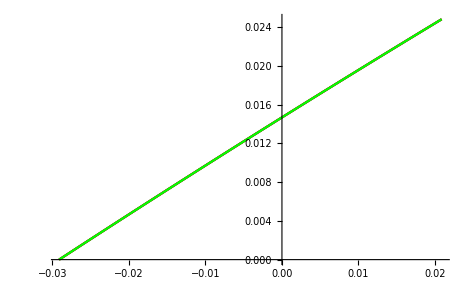

```mathematica
α=0;α0Plot=Plot[κ /. ϑ -> ϑPlot,{ϑPlot,ϑMin,ϑMin+0.05},PlotStyle->{Black}];
α=1;α1Plot=Plot[κ /. ϑ -> ϑPlot,{ϑPlot,ϑMin,ϑMin+0.05},PlotStyle->{Red}];
α=2;α2Plot=Plot[κ /. ϑ -> ϑPlot,{ϑPlot,ϑMin,ϑMin+0.05},PlotStyle->{Green}];
Show[α0Plot,α1Plot,α2Plot,PlotRange->All]
```

```mathematica
ÞRtn (1-℧)^(1+1/ρ)(1-α ℧)
```

0.932437 (1-0.005 α)

```mathematica
Clear[ϑ,𝔤,𝔊];
℧=0.01;
𝔊Min=(R)(1-℧);
𝔊Max=(R);
𝔊=(𝔊Min+𝔊Max)/2;
𝔤=𝔊-1;
ϑRequiredForTarget = ϑSeek /. (FindRoot[(((μ-1)/μ) -(ℛ-1)/ℛ) /. ϑ -> ϑSeek,{ϑSeek,ϑWhereGICHoldsExactly-0.001}]);
βThatExactlySatisfiesRIC=(R)^(ρ-1);
ϑThatExactlySatisfiesRIC=(βThatExactlySatisfiesRIC)^-1-1;
ϑMin=Max[ϑThatExactlySatisfiesRIC,ϑRequiredForTarget];
ϑGIC=ϑWhereGICHoldsExactly;
{ϑWhereGICHoldsExactly,ϑRequiredForTarget,ϑThatExactlySatisfiesRIC}
```

{-0.00961363,-0.0388592,-0.0291262}

```mathematica
{𝔊,(R)(1-℧)^(1/ρ)}
```

{1.02485,1.02484}

```mathematica
Π /. ϑ -> {ϑMin,ϑGIC}
```

{1.41868,2.01067}

```mathematica
κ /. ϑ -> {ϑMin,ϑGIC}
```

{0.,0.0099}

```mathematica
κ Π + ℛ^-1-1/. ϑ -> {ϑMin,ϑGIC}
```

{0.00505051,0.0249562}

```mathematica
κ /. ϑ -> {ϑMin,ϑGIC}
```

{0.,0.0099}

```mathematica
{ℛ κ Π/(1+ℛ κ Π), (μ-1)/μ} /.  ϑ -> {ϑGIC,ϑMin}
```

{{0.019421,0.},{0.019421,0.}}

```mathematica
{{(μ-1)/μ,(ℛ-1)/ℛ}}/.  ϑ -> {ϑMin,ϑGIC}
```

{{{0.,0.019421},-0.00505051}}

```mathematica
{{((R) β)(1-℧),(𝔊(1-℧)^-1)^ρ}
,{β,((𝔊(1-℧)^-1)^ρ)/((R) (1-℧))}
,{β,((𝔊(1-℧)^-1)^ρ)/((R) (1-℧))}
} /. ϑ -> {ϑMin,ϑGIC}
```

{{{1.05029,1.0296},1.07164},{{1.03,1.00971},1.05094},{{1.03,1.00971},1.05094}}

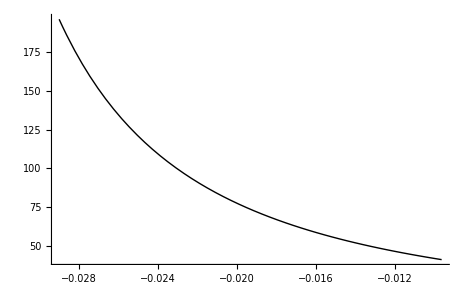

```mathematica
Plot[κ /. ϑ -> ϑPlot,{ϑPlot,ϑMin+0.0001,ϑGIC}]
```

```mathematica
{(ÞΓ^-ρ-1)
(*,(1+℘γ)^-ρ-1*)
,(1-ρ (ÞΓ-1))-1
,(1-ρ (ÞΓ-1)-ρ(-(ρ-1))(ÞΓ-1)^2/2)-1
,(1-ρ (ÞΓ-1)-ρ(-(ρ-1))(ÞΓ-1)^2/2-ρ(-(ρ-1))(-(ρ-2))(ÞΓ-1)^3/6)-1
,(- ρ (ÞΓ-1))} /. ϑ -> {ϑMin,ϑGIC}
```

{{0.0101265,0.030428},{0.0100503,0.0297508},{0.0100755,0.029972},{0.0100755,0.029972},{0.0100503,0.0297508}}

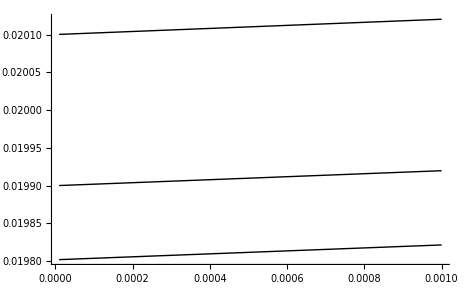

```mathematica
Plot[{
((1+(ÞΓ-1))^-ρ-1),
((1-ρ(ÞΓ-1)-1)),
((1-ρ(ÞΓ-1)-ρ(-(ρ-1)(ÞΓ-1)^2/2)-1))
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All]
```

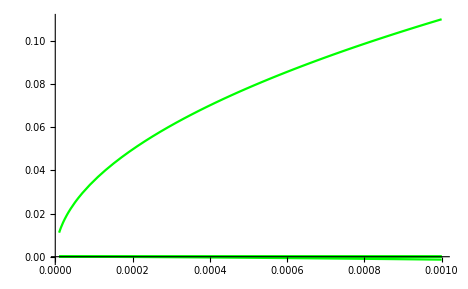

```mathematica
Plot[{
(*Π-((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
,*)
Π-((℧+((1+(ÞΓ-1))^-ρ-1))/℧)^(1/ρ)
,Π-((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
,Π-((1+(ÞΓ^-ρ-1)/℧))^(1/ρ)
,Π-(((ÞΓ^-ρ-1)/℧)(℧/(ÞΓ^-ρ-1)+1))^(1/ρ)
,Π-((ÞΓ^-ρ-1)/℧)^(1/ρ)((℧/(ÞΓ^-ρ-1)+1))^(1/ρ)
,Π-((ÞΓ^-ρ-1)/℧)^(1/ρ)(ρ^-1(℧/(ÞΓ^-ρ-1))+1)
,Π-((ÞΓ^-ρ-1)/℧)^(1/ρ)
(*,
Π-((℧+(1-ρ(ÞΓ-1)-1))/℧)^(1/ρ)*)
(*,Π-(℧+((1-ρ(ÞΓ-1)-ρ(-(ρ-1)(ÞΓ-1)^2/2))-1)/℧)^(1/ρ)*)
(*,Π-((℧+((1+℘γ)^-ρ-1))/℧)^(1/ρ)*)
(*,Π-(((- ρ (ÞΓ-1))+℧)/℧)^(1/ρ)*)
(*,Π-(((- ρ ℘γ)+℧)/℧)^(1/ρ)*)
(*,Π-(((- ρ ℘γ)/℧+1))^(1/ρ)*)
(*,Π-(((- ρ ℘γ)/℧)(1-(℧/( ρ ℘γ))))^(1/ρ)
,Π-((- ρ ℘γ)/℧)^(1/ρ)(1-(℧/( ρ ℘γ)))^(1/ρ)
,Π-((- ρ ℘γ)/℧)^(1/ρ)((1+(1/ρ)(℧/(- ρ ℘γ))))
,Π-((- ρ ℘γ)/℧)^(1/ρ)((1+(1/ρ)(℧/(- ρ ℘γ))+(1/ρ)((1/ρ)-1)(℧/(- ρ ℘γ))^2/2))*)
(*,Π-((- ρ ℘γ)/℧)^(1/ρ)((1-(℧/( ℘γ))))*)
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All,PlotStyle->{Red,Green}]
```

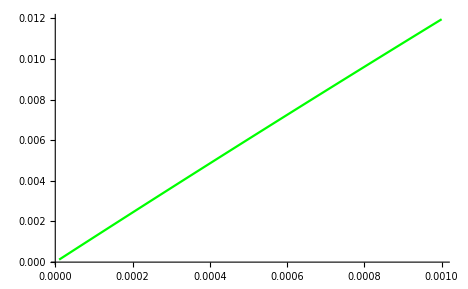

```mathematica
Plot[{
(℧/(ÞΓ^-ρ-1))
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All,PlotStyle->{Red,Green}]
```

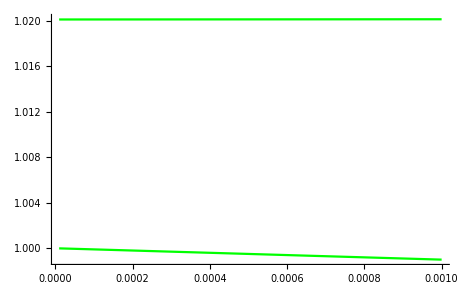

```mathematica
Plot[{
(1-℧)/. ℧ -> ℧Plot
,ÞΓ^-ρ
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All,PlotStyle->{Red,Green}]
```

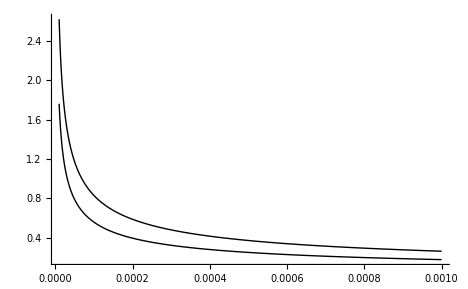

```mathematica
Plot[{
((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
-((℧+(1-ρ(ÞΓ-1)-1))/℧)^(1/ρ),
((℧+(ÞΓ^-ρ-1))/℧)^(1/ρ)
-((℧-ρ ℘γ)/℧)^(1/ρ)
} /. ℧ -> ℧Plot,{℧Plot,0.00001,0.001},PlotRange->All]
```

```mathematica
(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1
```

1.02074

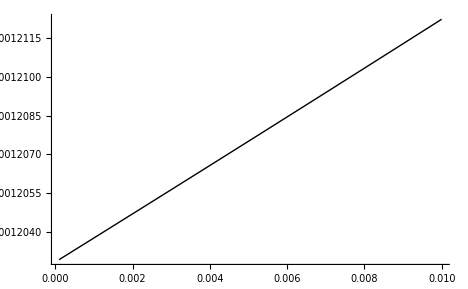

```mathematica
Plot[{℧((1-ÞRtn)((ÞΓ^-ρ-1)/℧)^(1/ρ))^ρ} /. ℧ -> ℧Plot,{℧Plot,0.0001,0.01},PlotRange->All]
```

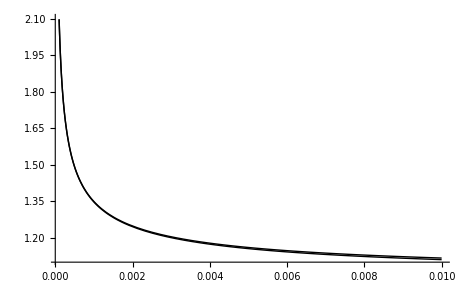

```mathematica
Plot[{(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1
,(1-ÞRtn)((ÞΓ^-ρ-1)/℧)^(1/ρ)+ℛ^-1} /. ℧ -> ℧Plot,{℧Plot,0.0001,0.01},PlotRange->All]
```

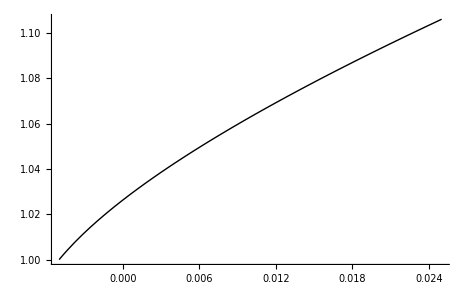

```mathematica
Plot[(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1 /. 𝔤 -> 𝔤Plot,{𝔤Plot,𝔤MinFromGIC,𝔤MaxFromFHWC}]
```

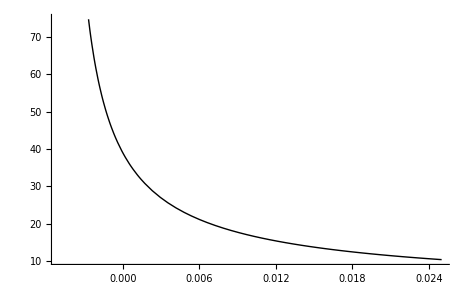

```mathematica
Plot[κ /. 𝔤 -> 𝔤Plot,{𝔤Plot,𝔤MinFromGIC,𝔤MaxFromFHWC}]
```

```mathematica
MatrixForm[{
{1,(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1}
,{1,(1-ÞRtn)((1+(1/ρ)ϖ))+ℛ^-1}
,{1,(1-ÞRtn)((1+(1/ρ)ϖ))+ℛ^-1}
,{1,(1-ÞRtn)+(1-ÞRtn)(1/ρ)ϖ+ℛ^-1}
,{0,-ÞRtn+(1-ÞRtn)(1/ρ)ϖ+ℛ^-1}
,{0,-ÞRtn+κ(1/ρ)ϖ+ℛ^-1}
,{ÞRtn,κ(1/ρ)ϖ+ℛ^-1}
,{ÞRtn,κ(1/ρ)ϖ+ℛ^-1}
,{Þ,κ(1/ρ)ϖ (R)+Γ}
,{Þ,κ(1/ρ)((1-ρ  ℘γ-1)/℧)(R)+Γ}
,{Þ,κ(1/ρ)((-ρ ℘γ)/℧)(R)+Γ}
,{Þ,κ((- ℘γ)/℧)(R)+Γ}
,{ÞΓ,κ((- ℘γ)/℧)ℛ+1}
,{ÞΓ-1,κ((- ℘γ)/℧)ℛ}
,{℘γ,κ((- ℘γ)/℧)ℛ}
} /. 𝔤 -> {𝔤MinFromGIC}]
```

(1 | {1.}
1 | {1.}
1 | {1.}
1 | {1.}
0 | {-1.11022×10^-16}
0 | {-1.11022×10^-16}
0.970874 | {0.970874}
0.970874 | {0.970874}
1. | {1.}
1. | {1.}
1. | {1.}
1. | {1.}
{1.} | {1.}
{-1.11022×10^-16} | {6.66134×10^-16}
{-1.11022×10^-16} | {6.66134×10^-16})

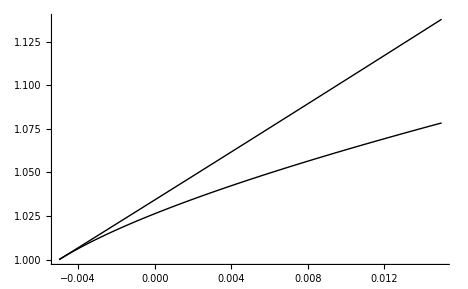

```mathematica
Plot[{(1-ÞRtn)(1+ϖ)^(1/ρ)+ℛ^-1 ,(1-ÞRtn)+(1-ÞRtn)(1/ρ)ϖ+ℛ^-1}/. 𝔤 -> 𝔤Plot,{𝔤Plot,𝔤MinFromGIC,𝔤MinFromGIC+0.02}]
```

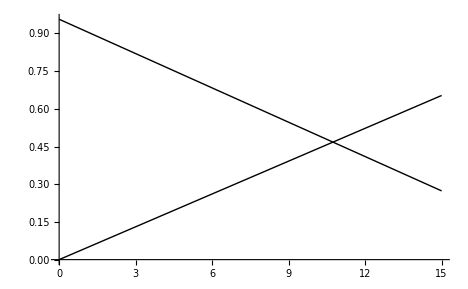

```mathematica
Plot[{((μ-1)/μ)m ,((ℛ^-1-1)/ℛ^-1)m+ℛ^-1 }/. r -> rMaxFromGIC,{m,0,15}]
```

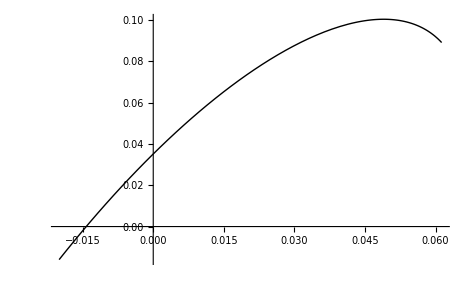

```mathematica
Plot[((μ-1)/μ)-((ℛ^-1-1)/ℛ^-1) /. r -> rPlot,{rPlot,-0.02,rMaxFromGIC}]
```

```mathematica
℧(ρ/(ρ-1))-ϑ/(ρ-1)
```

-0.02

```mathematica
μ
```

1+13.9321 (1+r) √(-0.995+1.06129/(1+r)) (1-0.985329/(√(1+r)))

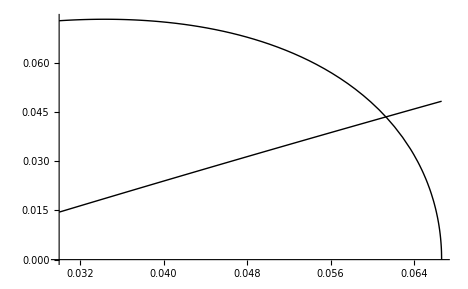

```mathematica
Plot[{(ζ/(1+ζ)),(1-ℛ^-1)} /. r -> rIndex,{rIndex,rMinFromRIC,rMaxFromGIC}]
```

```mathematica
rMaxFromGIC
```

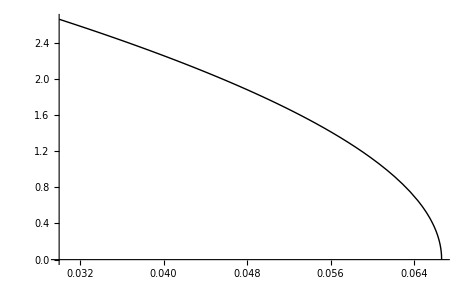

```mathematica
Plot[Π /. r -> rIndex,{rIndex,rMin,rMaxFromGIC}]
```

```mathematica
Π /. r -> rMaxThatGeneratesSS
```

1.

```mathematica
{κ
```

1-0.985329/(√(1+r))

```mathematica
ÞΓ /. r -> rMaxThatGeneratesSS
```

1.

```mathematica
Clear[r];MatrixForm[{{ζ/(1+ζ),">",(1-ℛ^-1)}
,{ℛ ζ/(1+ζ),">",(ℛ-1)}
,{ℛ ((ζ/(1+ζ))-1)+1,">",0}
,{ℛ ((ζ/(1+ζ))-1)+1,">",0}
,{ℛ ((ζ/(1+ζ))-1),">",-1}
,{ℛ (1-(ζ/(1+ζ))),"<",1}
,{ℛ ((1)-(ζ/(1+ζ))),"<",1}
,{ℛ (((1+ζ)/(1+ζ))-(ζ/(1+ζ))),"<",1}
,{ℛ (1/(1+ζ)),"<",1}
,{ℛ ,"<",1+ζ}
,{ℛ ,"<",1+ℛ κ Π }
,{ℛ ,"<",1+ℛ  (1-ÞRtn) Π}
,{ℛ ,"<",1+  (ℛ-ÞΓ) Π}
,{ℛ (1-Π),"<",1 -ÞΓ Π}
}]/. r ->{rMaxThatGeneratesSS-0.001,rMaxThatGeneratesSS+0.001}
```

({0.0467801,0.0398296} | > | {0.0426431,0.0444455}
{0.0488638,0.0416821} | > | {0.0445425,0.0465128}
{0.0043213,-0.00483065} | > | 0
{0.0043213,-0.00483065} | > | 0
{-0.995679,-1.00483} | > | -1
{0.995679,1.00483} | < | 1
{0.995679,1.00483} | < | 1
{0.995679,1.00483} | < | 1
{0.995679,1.00483} | < | 1
{1.04454,1.04651} | < | {1.04908,1.04148}
{1.04454,1.04651} | < | {1.04908,1.04148}
{1.04454,1.04651} | < | {1.04908,1.04148}
{1.04454,1.04651} | < | {1.04908,1.04148}
{-0.0942617,0.103648} | < | {-0.0897283,0.0986165})

```mathematica
(* Successive approximations to Π *)
MatrixForm[{{1,Π-(1+(ÞΓ^-ρ-1)/℧)^(1/ρ)}
,{2,Π-(1+((1+(ÞΓ-1))^-ρ-1)/℧)^(1/ρ)}
,{3,Π-(1+ρ^-1(((1+(ÞΓ-1))^-ρ-1)/℧))}
,{4,Π-(1+ρ^-1(((1-ρ(ÞΓ-1)-ρ(-ρ-1)((ÞΓ-1)^2/2))-1)/℧))}
,{5,Π-(1+ρ^-1(((1-ρ (ρ^-1(r-ϑ)-γ))-1)/℧))}
,{6,Π-(1+ρ^-1(((1- ((r-ϑ)-ρ γ))-1)/℧))}
,{7,Π-(1+ρ^-1((ÞΓ^-ρ-1)/℧)+ρ^-1(ρ^-1-1)((ÞΓ^-ρ-1)/℧)^2/2)}
,{8,Π-(1+ρ^-1(((1-ρ(ÞΓ-1))-1)/℧)+ρ^-1(ρ^-1-1)(((1-ρ(ÞΓ-1))-1)/℧)^2/2)}
,{9,Π-(1+ρ^-1(((1-ρ ℘γ)-1)/℧)+ρ^-1(ρ^-1-1)(((1-ρ ℘γ)-1)/℧)^2/2)}
,{10,Π-(1+ρ^-1(((-ρ ℘γ)/℧)+ρ^-1(ρ^-1-1)(((-ρ ℘γ))/℧)^2/2))}
}
]/. r ->  {rMaxThatGeneratesSS-0.005,rMaxThatGeneratesSS,rMaxThatGeneratesSS+0.005}
```

(1 | {4.44089×10^-16,4.44089×10^-16,1.80411×10^-15}
2 | {4.44089×10^-16,4.44089×10^-16,1.80411×10^-15}
3 | {-0.0781095,4.44089×10^-16,-0.281748}
4 | {-0.0781043,4.44089×10^-16,-0.281754}
5 | {0.0316072,0.136362,-0.114303}
6 | {0.0316072,0.136362,-0.114303}
7 | {0.033923,4.44089×10^-16,-0.171807}
8 | {0.0348059,4.44089×10^-16,-0.169374}
9 | {0.0345118,4.44089×10^-16,-0.170187}
10 | {-0.0212405,4.44089×10^-16,-0.225416})

```mathematica
rHatMaxThatGeneratesSS = rHatFind /.(FindRoot[ℛ (ΠHat-1) -(1-(1+(ρ^-1(r-ϑ)-γ)/℧) ΠHat) /. r -> rHatFind,{rHatFind,rMaxThatGeneratesSS-0.001}]) ;
{rMaxThatGeneratesSS,rHatMaxThatGeneratesSS}
```

{0.0612894,0.0599257}

```mathematica
Clear[r];FindRoot[ℛ(1-ΠHat) -(1-(1+℘γApprox) ΠHat) /. r -> rSeek ,{rSeek,rMaxFromGIC}]
```

{rSeek→0.0599257}

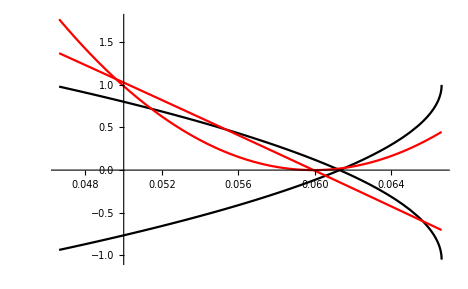

```mathematica
(* Unfortunately, if we go very far from the truth the approximation is poor; actually there are multiple solutions  *)
Plot[{ℛ(Π-1) /. r -> rIndex,1-ÞΓ Π/. r -> rIndex,ℛ (ΠHat-1) /. r -> rIndex, 1-(1+(ρ^-1(r-ϑ)-γ)/℧) ΠHat /. r -> rIndex } ,{rIndex,rMaxFromGIC-0.02,rMaxFromGIC},PlotStyle->{Black,Black,Red,Red}]
```

```mathematica
(* Find the approximate analytical solution *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Get["../../CoreCode/Autoload/init.m"];
Get["../../CoreCode/MakeAnalyticalResults.m"];
Get["../../CoreCode/VarsAndFuncs.m"];
(* Define ΠHat as one of the approximations derived below; needs to be defined here to remain analytical/dynamic *)
℘γApprox=(ρ^-1(r-ϑ)-γ);
Clear[r];(*ΠHat=(1+ρ^-1(((-ρ ℘γ)/℧)));*)
ΠHat=(1- ℘γApprox/℧);
(*ΠHat=(1+ρ^-1(((1-ρ(ÞΓ-1))-1)/℧)+ρ^-1(ρ^-1-1)(((1-ρ(ÞΓ-1))-1)/℧)^2/2);*)
ζHat=ℛ κ ΠHat; 
(* If the starting point is close to the truth, then it finds the right answer *)
```

```mathematica
Clear[r];Solve[ℛ (ΠHat-1)-(1-(1+℘γApprox/℧) ΠHat)==0,{r}]
```

{{r→ϑ+ρ Log[(1+𝔤)/(1-℧)]},{r→(ϑ+𝔤 ϑ-ρ ℧+ρ ℧^2+ρ Log[(1+𝔤)/(1-℧)]+𝔤 ρ Log[(1+𝔤)/(1-℧)])/(1+𝔤+ρ ℧-ρ ℧^2)}}

```mathematica
Severance=PDies=τ=0;𝔤=𝔤Min=0.01;ρ=ρBase=2;ϑ=ϑBase=0.03;℧=℧Base=0.005;𝔤Gap=0.01;
rMinFromFHWC=𝔤Min + ℧;
rMinFromRIC=ϑ/(ρ-1);
rMin=Max[rMinFromFHWC,rMinFromRIC];
rMaxFromGICApprox=ρ 𝔤Min + ℧(ρ+1)+ϑ;
rMaxFromGIC=𝔊^ρ/(β(1-℧)^(ρ+1))-1;
(* For any r greater than this, no SS exists *)
rMaxThatGeneratesSS = rFind /.(FindRoot[ ζ/(1+ζ) - (1-ℛ^-1) /. r -> rFind,{rFind,rMin+0.001}]) ;
{rMaxFromGICApprox,rMaxFromGIC,rMaxThatGeneratesSS};Solve[ℛ (ΠHat-1)-(1-(1+℘γApprox/℧) ΠHat)==0,{r}]
```

{{r→0.0495858},{r→0.0599257}}

```mathematica
{ρ^-1(r-ϑ)-(𝔤+℧)<ρ^-1℧
,(r-ϑ)<℧+ρ(𝔤+℧)
,r<ϑ + ℧(ρ+1)+ρ 𝔤
,(ρ^-1(r-ϑ)-r)<0
,r (ρ^-1-1)-ϑ ρ^-1<0
,r ρ^-1(1-ρ)<ϑ ρ^-1
,r (1-ρ)-ϑ<0
,r (ρ-1)+ϑ >0
,r (ρ-1)>-ϑ
,r>𝔤}

{-0.015+1/2 (-0.03+r)<0.0025,-0.03+r<0.034999999999999996,r<0.065,1/2 (-0.03+r)-r<0,-0.015-r/2<0,-r/2<0.015,-0.03-r<0,0.03+r>0,r>-0.03,r>0.01}
{(((R) β)^(1/ρ))/(𝔊/(1-℧))<(1-℧)^(-1/ρ)
,
(((R) β)^(1/ρ))(1-℧)/𝔊<(1-℧)^(-1/ρ)
,
(((R) β)^(1/ρ))(1-℧)^(1+1/ρ)/𝔊<1
,
(((R) β)^(1/ρ))(1-℧)^((ρ+1)/ρ)𝔊^-1<1
,
((R) β)(1-℧)^(ρ+1)𝔊^-ρ<1
,
((R) β)<𝔊^ρ(1-℧)^(-(ρ+1))
,
(R) <𝔊^ρ/(β(1-℧)^(ρ+1))
}

{True,True,True,True,True,True,True}
```

```mathematica
MatrixForm[{{ζ/(1+ζ),(1-ℛ^-1)}
,{ζ/(1+ζ),(ℛ-1)/ℛ}
,{ℛ ζ,(1+ζ)(ℛ-1)}
,{ℛ ζ,(1+ζ)(ℛ-1)}
,{ℛ ζ,ℛ + ℛ ζ-(1+ζ)}
,{0,ℛ -(1+ζ)}
,{(1+ζ),ℛ }
,{1+ℛ (1-ÞRtn)Π,ℛ }
,{1+ℛ (1-ÞRtn)Π,ℛ }
}]/. r -> rMaxThatGeneratesSS-0.01
```

(0.0643932 | 0.0344472
0.0643932 | 0.0344472
0.0712804 | 0.0381316
0.0712804 | 0.0381316
0.0712804 | 0.0381316
0 | -0.0331489
1.06883 | 1.03568
1.06883 | 1.03568
1.06883 | 1.03568)

```mathematica
Π /. r -> rMax
```

14.1421 √(-0.995+1.06129/(1+r))